# Mathematica HomeWork

中山大学物理学院 李子锋

## 1. Basic Calculations

1.1.1 Getting Started

1. Use the Basic Input palette to type in the expression 3100 below this cell. Hit ⇧|⏎ together to evaluate this expression. Note that you should get the exact answer.

```mathematica
3^100
```

515377520732011331036461129765621272702107522001

2. Select your input line above (either by selecting its Computational Biophysics cell bracket or by scrolling over the expression with the mouse clicked) and make a copy using Copy
under the Edit menu. Paste your expression below this box. Change the 100 to 1000 and evaluate the result.

```mathematica
3^1000
```

1322070819480806636890455259752144365965422032752148167664920368226828597346704899540778313850608061963909777696872582355950954582100618911865342725257953674027620225198320803878014774228964841274390400117588618041128947815623094438061566173054086674490506178125480344405547054397038895817465368254916136220830268563778582290228416398307887896918556404084898937609373242171846359938695516765018940588109060426089671438864102814350385648747165832010614366132173102768902855220001

3. To get the result in the form you might get on a calculator, try N[%].

```mathematica
N[%]
```

1.32207081948081×10^477

4. Enter pi = N[π, 200] below this cell and evaluate it

```mathematica
pi=N[Pi,200]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117067982148086513282306647093844609550582231725359408128481117450284102701938521105559644622948954930382

5. Enter ⅇ163 pi3 below this cell and evaluate it. What is special about this number?

```mathematica
E^(√163 Pi/3)
```

ⅇ^((√163 π)/3)

```mathematica
N[ⅇ^((√163 π)/3),200]
```

640320.00000000060486373504901603947174181881853947577148576036659181946522182582869425363408158226464775899925470001727925679647867303997506923198495665261269396826561338913713441824901972334433095988

Nothing special

6. π has a run of six consecutive 9’s in the first 1000 digits. Can you see where they are located? (One way to find the location is to convert the number to a 2 HomeWork.nb string [using ToString], drop the leading 3. [using StringDrop] and locating the position of the string “999999” [using StringPosition]).

```mathematica
ToString[N[Pi]]
```

3.14159

```mathematica
StringPosition[ToString[N[Pi,1000]],"999999"]
```

{{764,769}}

1.1.2 More Functions

7. Compute sin(13 π), log(2.1), and ⅇⅈ π by copying these expressions below this cell and entering them.

```mathematica
MatrixForm[{Sin[13 Pi],Log[2,1],E^(I Pi)}]
```

(0
0
-1)

8. Lookup cos in the on-line help and determine closed-form expressions for cos( π5 ).

```mathematica
Cos[Pi/5]
```

1/4 (1+√5)

9. Evaluate FactorInteger[70 612 139 395 722 186]. What is the meaning of this output?

```mathematica
FactorInteger[70612139395722186]
```

{{2,1},{3,2},{43,5},{26684839,1}}

2 times 3 to the power of 2 times 43 to the power of 5 times 26684839 equals to that.

10. Recombine the numbers in the above output to show how they form 70 612 139 395 722 186.

```mathematica
2^1 3^2 43^5 26684839
```

70612139395722186

1.1.3 Simple Expressions

11. Enter the expression (x2 + 2 x + 1)20. Expand this 

expression using Expand[%]. Factor the expanded 

result.

```mathematica
expres1=(x^2+2x+1)^20;
Expand[expres1]
```

1+40 x+780 x^2+9880 x^3+91390 x^4+658008 x^5+3838380 x^6+18643560 x^7+76904685 x^8+273438880 x^9+847660528 x^10+2311801440 x^11+5586853480 x^12+12033222880 x^13+23206929840 x^14+40225345056 x^15+62852101650 x^16+88732378800 x^17+113380261800 x^18+131282408400 x^19+137846528820 x^20+131282408400 x^21+113380261800 x^22+88732378800 x^23+62852101650 x^24+40225345056 x^25+23206929840 x^26+12033222880 x^27+5586853480 x^28+2311801440 x^29+847660528 x^30+273438880 x^31+76904685 x^32+18643560 x^33+3838380 x^34+658008 x^35+91390 x^36+9880 x^37+780 x^38+40 x^39+x^40

12. Re-do the steps in the above computation using 

the Basic Calculations palette.

```mathematica
(x^2+2x+1)^2
```

(1+2 x+x^2)^2

TrigReduce[sin(x) cos(y) - cos(x) sin(y)] and apply TrigExpand to the result. What can you say about the relationship between these functions?

```mathematica
Clear[x,y]
TrigReduce[Sin[x]Cos[y]-Cos[x]Sin[y]]
```

Sin[x-y]

```mathematica
TrigExpand[%]
```

Cos[y] Sin[x]-Cos[x] Sin[y]

两个函数互为逆运算

1.1.4 Basic Plots

14. Produce a plot of sin(x2) over x ∈ [0, 5]

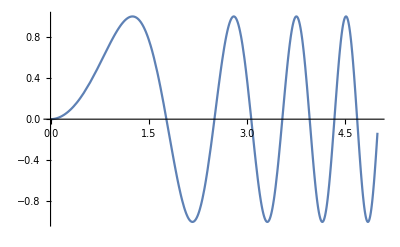

```mathematica
Plot[Sin[x^2],{x,0,5}]
```

15. Produce a phase-space plot of cos(x) versus sin(3 x) for over x ∈ [0, 2 π].

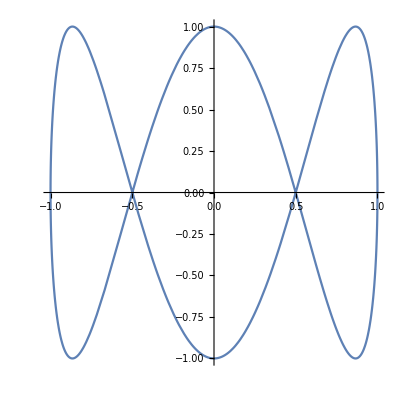

```mathematica
ParametricPlot[{Cos[x],Sin[3 x]},{x,0,2Pi}]
```

16. Produce a contour plot and density plot of x ⅇ-x2-y2 4 HomeWork.nb for -1 ≤ x ≤ 1 and -1 ≤ y ≤ 1

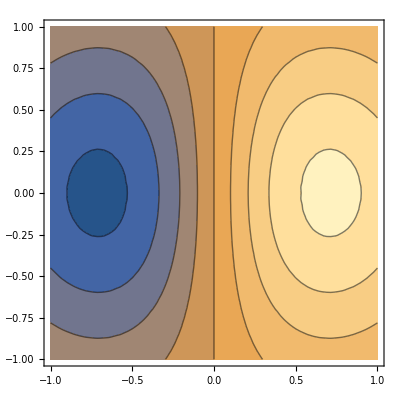

```mathematica
Clear[x,y];
ContourPlot[x E^(-x^2-y^2),{x,-1,1},{y,-1,1}]
```

1.1.5 Calculus

1.1.6 Solving Equations

1.1.7 Matrices

1.1.8 Curve Fitting